```mathematica
P1[x_,h_]:=BernoulliB[1,x/h-Abs[x/h]]
```

```mathematica
BernoulliB[2,x/h-Floor[x/h]]
```

1/6-x/h+(x/h-Floor[x/h])^2+Floor[x/h]

```mathematica
1/6-x/h+(x/h-k/h)^2+k/h
```

```mathematica
Evaluate[BernoulliB[2,x/h-Floor[x/h]] ]/. Floor[x/h]-> k/h
```

1/6+k/h-x/h+(-k/h+x/h)^2

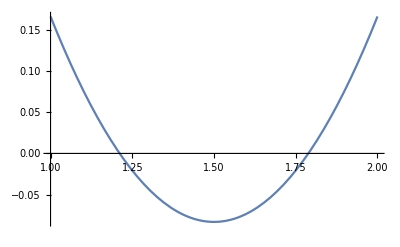

```mathematica
Plot[1/6-x/h+(x/h-k/h)^2+k/h/.k->1/.h->1,{x,1,2}]
```

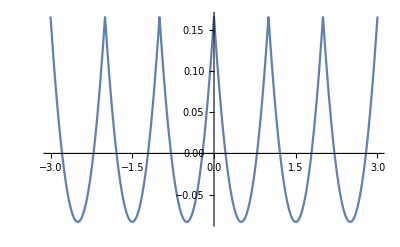

```mathematica
Plot[1/6-x/h+(x/h-Floor[x/h])^2+Floor[x/h]/.h->1 ,{x,-3,3}]
```

```mathematica
Plot[BernoulliB[2,x/h-Floor[x/h]] /.h->1,{x,-3,3}]
```

-Graphics-

```mathematica
P[x_,h_]:=BernoulliB[1,x/h-Abs[x/h]]
```

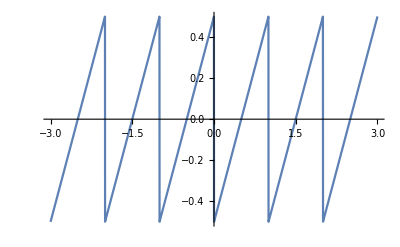

```mathematica
Plot[BernoulliB[1,x/h-Floor[x/h]] /.h->1,{x,-3,3}]
```

```mathematica
Evaluate[BernoulliB[1,x/h-Floor[x/h]] ]/. Floor[x/h] -> k/h
```

-1/2-k/h+x/h

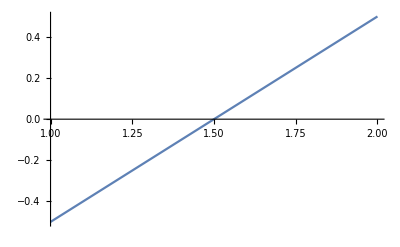

```mathematica
Plot[-1/2-k/h+x/h/.k->1/.h-> 1,{x,1,2}]
```

```mathematica
∫_k^(k+h) (-1/2-k/h+x/h)ⅆx
```

0

```mathematica
∫_k^(k+h) (-1/2-k/h+x/h)(x-k)ⅆx
```

h^2/12

```mathematica
∫_k^(k+h) (-1/2-k/h+x/h)(x-k)^2 ⅆx
```

h^3/12

```mathematica
Series[Erfc[n(g2-x)+2π ⅈ s]-Erfc[n(g2-x)-2π ⅈ s],{s,0,3}]
```

-8 ⅈ ⅇ^(-n^2 (g2-x)^2) √π s+16/3 ⅈ ⅇ^(-n^2 (g2-x)^2) π^(5/2) (-2+(2 g2 n-2 n x)^2) s^3+O[s]^4

```mathematica
PadeApproximant[Normal[-8 ⅈ ⅇ^(-n^2 (g2-x)^2) √π s+16/3 ⅈ ⅇ^(-n^2 (g2-x)^2) π^(5/2) (-2+(2 g2 n-2 n x)^2) s^3+O[s]^4],{s,0,2}]
```

```mathematica
CDF[NormalDistribution[0,1/(√n)],n(g2-x)+2π ⅈ n  s]+CDF[NormalDistribution[0,1/(√n)],n(g2-x)-2π ⅈ n s] /. n-> 23.1 /. g2-> 1.3 /. x-> 0.3 /. s-> π
```

4.27834229421602×10^1040235+0``-1040221.1486105329 ⅈ

```mathematica
1/(2ⅈ)(CDF[NormalDistribution[0,1/(√n)],n(g2-x)+n 2π ⅈ s]-CDF[NormalDistribution[0,1/(√n)],n(g2-x)-n 2π ⅈ s]) /. n-> 30 /. g2-> 1.3 /. x-> 0 /. s-> π //N
```

1.02312974104785×10^2274516+0``-2274499.9636671892 ⅈ

```mathematica
Series[1/(2ⅈ)(CDF[NormalDistribution[0,1/(√n)],n(g2-x)+2π ⅈ s]-CDF[NormalDistribution[0,1/(√n)],n(g2-x)-2π ⅈ s]),{s,0,3}]
```

ⅇ^(-1/2 n^3 (g2-x)^2) √n √(2 π) s-2/3 (√2 ⅇ^(-1/2 n^3 (g2-x)^2) n^(3/2) π^(5/2) (-1+g2^2 n^3-2 g2 n^3 x+n^3 x^2)) s^3+O[s]^4